# Number of Sampled Infections

```mathematica
i01=3;
```

```mathematica
Clear[contours2]
```

```mathematica
parsTest0:={β->0.2,γ->0.01,ψ->0.01,σ->0.001,κ->300, tMax->100,i0->i01, ρ ->0}; 
parsTest1:={β->0.1,γ->0.01,ψ->0.01,σ->0.001,κ->300, tMax->100,i0->i01, ρ ->1};
parsTest5:={β->0.1,γ->0.01,ψ->0.01,σ->0.001,κ->300, tMax->100,i0->i01, ρ ->0.5};

parsTest = parsTest1;
contours={2,4,10,20,40,100};
contours2[scale_]:=scale{2,4,10,20,40,100};
```

```mathematica
MyCol=Table[ColorData["DarkBands"][i/6-0.01],{i,1,6}]
```

{RGBColor[0.23132947583985186, 0.5230171758179645, 0.6762635983204028],RGBColor[0.30222321343557096, 0.5283591583672841, 0.26781478622442834],RGBColor[0.6416497175320824, 0.22039024680361508, 0.2965244160637617],RGBColor[0.6953106517659292, 0.4338224431042085, 0.2550317501625878],RGBColor[0.3208696220556491, 0.33272406933605325, 0.551604665638763],RGBColor[0.8884240140546887, 0.8315410617160953, 0.3918643845410284]}

## Stochastic “True” Distribution

```mathematica
Clear[Events]
```

```mathematica
Events[Δt_]:={{Δt,-1,1,0,0,1},{Δt,0,-1,1,0,0},{Δt,0,0,0,1,0},{Δt,0,-1,1,1,0},{Δt,1,0,-1,0,0}};
Rates[state_]:={β/κ state[[2]]state[[3]],γ state[[3]],(1-ρ)ψ state[[3]],ρ ψ state[[3]],σ state[[4]]};
```

```mathematica
Clear[sim]
sim[pars_,intS_]:=sim[pars,intS]=Block[{out,Δt,temp,t,event},
out={{0,κ-i0,i0,0,0,i0}}/.pars;
temp=Rates[out[[-1]]]/.pars;
Δt=RandomVariate[ExponentialDistribution[Total[temp]]];
While[(out[[-1,1]]+Δt&&out[[-1,3]]>0)<(tMax/.pars),
event=RandomChoice[temp->{1,2,3,4,5}];
AppendTo[out,out[[-1]]+Events[Δt][[event]]];
temp=Rates[out[[-1]]]/.pars;
Δt=RandomVariate[ExponentialDistribution[Total[temp]]];
];
AppendTo[out,Join[{tMax/.pars},out[[-1,2;;]]]];
out
]
```

```mathematica
Clear[simInt]
simInt[pars_,intS_,var_]:=simInt[pars,intS,var]=Interpolation[sim[pars,intS][[;;,{1,var+1}]],InterpolationOrder->0]
```

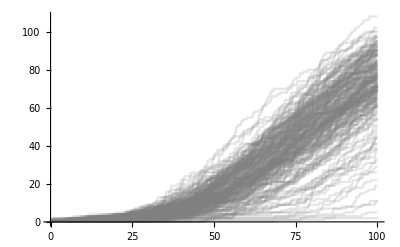

```mathematica
Plot[Evaluate[Table[simInt[parsTest,intS,4][x],{intS,1,200}]],{x,0,tMax/.parsTest},PlotRange->All,PlotStyle->Directive[Gray,Opacity[0.2]]]
```

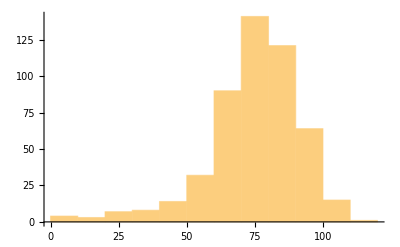

```mathematica
Histogram[Table[simInt[parsTest,intS,4][tMax/.parsTest],{intS,1,500}]]
```

# Simulation Based Estimates

```mathematica
(*Calculate the number of infections for a given RApproximent and γ*)
stoMeanSamp[RA_,g_,κIn_,tM_,i0in_,ρin_]:=Block[{parsSim},
parsSim={β->RA g,γ->g,ψ->(ψ/.parsTest),σ->0.001,κ->κIn,tMax->tM,i0->i0in,ρ->ρin};
Mean[Table[simInt[parsSim,intS,4][tMax/.parsSim],{intS,1,100}]]//N
]
```

```mathematica
stoMeanSamp[5,0.05,300,100,3,1]
```

49.26

```mathematica
(*Calculate the total number of infections for a given RApproximent and γ*)
stoMeanTot[RA_,g_,κIn_,tM_,i0in_,ρin_]:=Block[{parsSim},
parsSim={β->RA g,γ->g,ψ->(ψ/.parsTest),σ->0.001,κ->κIn,tMax->tM,i0->i0in,ρ->ρin};
Mean[Table[simInt[parsSim,intS,5][tMax/.parsSim],{intS,1,100}]]//N
]
```

```mathematica
stoMeanTot[5,0.05,300,100,3,1]
```

```mathematica
(*Calculate the variance of infections for a given RApproximent and γ*)
stoVarSamp[RA_,g_,κIn_,tM_,i0in_,ρin_]:=Block[{parsSim},
parsSim={β->RA g,γ->g,ψ->(ψ/.parsTest),σ->0.001,κ->κIn,tMax->tM,i0->i0in,ρ->ρin};
Variance[Table[simInt[parsSim,intS,4][tMax/.parsSim],{intS,1,200}]]//N
]
```

```mathematica
(*Calculate the variance of infections for a given RApproximent and γ*)
stoVarTot[RA_,g_,κIn_,tM_,i0in_,ρin_]:=Block[{parsSim},
parsSim={β->RA g,γ->g,ψ->(ψ/.parsTest),σ->0.001,κ->κIn,tMax->tM,i0->i0in,ρ->ρin};
Variance[Table[simInt[parsSim,intS,5][tMax/.parsSim],{intS,1,200}]]//N
]
```

```mathematica
(*Calculate the coefficeint of variation of infections for a given RApproximent and γ*)
stoCVSamp[RA_,g_,κIn_,tM_,i0in_,ρin_]:=Block[{parsSim},
parsSim={β->RA g,γ->g,ψ->(ψ/.parsTest),σ->0.001,κ->κIn,tMax->tM,i0->i0in,ρ->ρin};
(Variance[Table[simInt[parsSim,intS,4][tMax/.parsSim],{intS,1,200}]]//N)/(Mean[Table[simInt[parsSim,intS,4][tMax/.parsSim],{intS,1,200}]]//N)

]
```

```mathematica
(*Calculate the coefficeint of variation of infections for a given RApproximent and γ*)
stoCVTot[RA_,g_,κIn_,tM_,i0in_,ρin_]:=Block[{parsSim},
parsSim={β->RA g,γ->g,ψ->(ψ/.parsTest),σ->0.001,κ->κIn,tMax->tM,i0->i0in,ρ->ρin};
(Variance[Table[simInt[parsSim,intS,5][tMax/.parsSim],{intS,1,200}]]//N)/(Mean[Table[simInt[parsSim,intS,5][tMax/.parsSim],{intS,1,200}]]//N)

]
```

## Grid of beta and gamma values:

```mathematica
(*Calculate grid of observed epidemic sizes*)
grid[eleFun_,κIn_,tM_,i0in_,ρin_]:=Flatten[Table[{R0,g,eleFun[R0,g,κIn,tM,i0in,ρin]},{R0,1.,5.,4/6},{g,0.05,0.5,0.5/6}],1]
(*Plot Grid*)
SizePlot[grid_,Style_]:=ListContourPlot[grid,Contours->contours,ContourStyle->Table[Directive[Join[Style,{ColorData["RedBlueTones"][(6-c)/6],Opacity[1]}]],{c,1,6}],ContourShading->False,PlotLegends->BarLegend[Automatic],ContourLabels->True,FrameLabel->{,}]
SizePlot2[grid_,Style_,scale_]:=ListContourPlot[grid,Contours->contours2[scale],ContourStyle->Table[Directive[Join[Style,{ColorData["RedBlueTones"][(6-c)/6],Opacity[1]}]],{c,1,6}],ContourShading->False,PlotLegends->BarLegend[Automatic],ContourLabels->True,FrameLabel->{,}]
```

```mathematica
(*Calculate grid of observed epidemic sizes*)
grid2[eleFun_,κIn_,tM_,i0in_,ρin_]:=Flatten[Table[{R0,g,eleFun[R0,g,κIn,tM,i0in,ρin]},{R0,1.,5.,4/6},{g,0.01,0.05,0.01}],1]
(*Plot Grid*)
SizePlot[grid_,Style_]:=ListContourPlot[grid,Contours->contours,ContourStyle->Table[Directive[Join[Style,{ColorData["RedBlueTones"][(6-c)/6],Opacity[1]}]],{c,1,6}],ContourShading->False,PlotLegends->BarLegend[Automatic],ContourLabels->True,FrameLabel->{,}]
SizePlot2[grid_,Style_,scale_]:=ListContourPlot[grid,Contours->contours2[scale],ContourStyle->Table[Directive[Join[Style,{ColorData["RedBlueTones"][(6-c)/6],Opacity[1]}]],{c,1,6}],ContourShading->False,PlotLegends->BarLegend[Automatic],ContourLabels->True,FrameLabel->{,}]
```

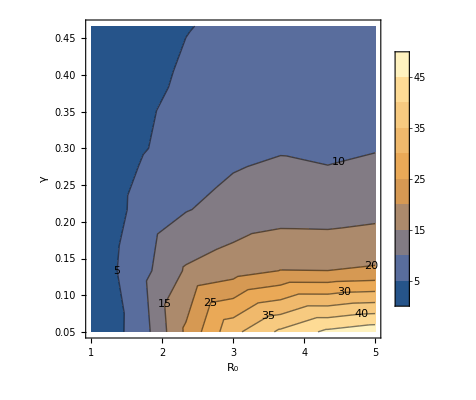

```mathematica
ListContourPlot[grid[stoMeanSamp,κ/. parsTest,tMax/. parsTest,3,1],PlotLegends->BarLegend[Automatic],ContourLabels->True,FrameLabel->{,}]
```

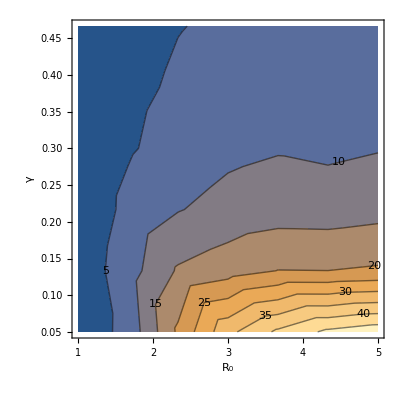

```mathematica
ListContourPlot[grid[stoMeanSamp,κ/. parsTest,tMax/. parsTest,3,1],ContourLabels->True,FrameLabel->{,}]
```

```mathematica
Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/manuscript/Figures/mean_sampled_sto.png",%]
```

/Users/siavashriazi/Dropbox/Apps/Overleaf/manuscript/Figures/mean_sampled_sto.png

## Deterministic estimate

Defining dS/st, dI/dt and dR/dt:

d/dt S[t]=f1[t], d/dt i[t]=f2[t], d/dt r[t]=f3[t],d/dt l[t]=f4[t],d/dt b[t]=f5[t]

Differential equations:

```mathematica
f1[t_]:=-β s[t] i[t]/κ+σ r[t]
f2[t_]:=β s[t] i[t]/κ-γ i[t]-ρ ψ i[t]
f3[t_]:=(γ+ρ ψ)i[t]-σ r[t]
f4[t_]:=ψ i[t]
f5[t_]:=β s[t] i[t]/κ
```

```mathematica
odes[pars_]:={D[s[t2],t2]==f1[t2],D[i[t2],t2]==f2[t2],D[r[t2],t2]==f3[t2], D[l[t2],t2]==f4[t2],D[b[t2],t2]==f5[t2],s[0]==κ-i0,i[0]==i0,r[0]==0,l[0]==0,b[0]==i0}/.pars;
vars={s[t2],i[t2],r[t2],l[t2],b[t2]};
```

```mathematica
Clear[nsol]
nsol[pars_]:=nsol[pars]=NDSolve[odes[pars],vars,{t2,0,tMax/.pars}][[1]]
```

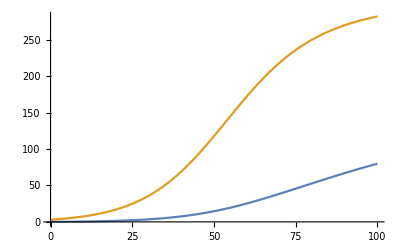

```mathematica
Plot[{l[t2]/.nsol[parsTest]/.t2->t,b[t2]/.nsol[parsTest]/.t2->t},{t,0,100}]
```

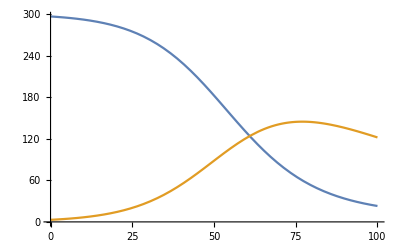

```mathematica
Plot[{s[t2]/.nsol[parsTest]/.t2->t,i[t2]/.nsol[parsTest]/.t2->t},{t,0,100}]
```

```mathematica
(*Calculate the number of infections for a given RApproximent and γ*)
detSamp[RA_,g_,κIn_,tM_,i0in_,ρin_]:=Block[{parsSim},
parsSim={β->RA g,γ->g,ψ->(ψ/.parsTest),σ->0.001,κ->κIn,tMax->tM,i0->i0in, ρ-> ρin};
(*NIntegrate[Evaluate[i[t2]/. nsol[parsSim]/.t2->t]*(ψ/. parsSim),{t,0,tM}];*)
(l[t2]/.nsol[parsSim])/.t2->tM
]
```

```mathematica
detSamp[2,0.01,κ/.parsTest,100,i01,ρ01]
```

2.95151

```mathematica
detTot[RA_,g_,κIn_,tM_,i0in_,ρin_]:=Block[{parsSim},
parsSim={β->RA g,γ->g,ψ->(ψ/.parsTest),σ->0.001,κ->κIn,tMax->tM,i0->i0in,ρ->ρin };
(b[t2]/.nsol[parsSim])/.t2->tM
]
```

## Numerical Integration of dp_n/dt

NOTE: I should check the sampling, is it psi or (1-rho)*psi

```mathematica
f[n_,τ_]:=λ[τ] Sum[p[k,τ]p[n-k,τ],{k,0,n}]+If[n==0,μ,If[n==1,ψ,0]]-(λ[τ]+ψ+μ)p[n,τ]
```

```mathematica
odesDiv[pars_,nMax_]:=Table[D[p[n,τ],τ]==f[n,τ],{n,0,nMax}]/.parsD[pars,τ]
initsDiv[nMax_]:=Table[If[n==0,p[n,0]==1,p[n,0]==0],{n,0,nMax}]
varsDiv[nMax_]:=Table[p[n,τ],{n,0,nMax}]
```

```mathematica
parsD[pars_,τ_]:={λ[τ]->β/κ s[t2]/.nsol[pars]/.{t2->tMax-τ}/.pars,μ->γ/.pars,ψ->(ψ/.pars)}
```

```mathematica
parsD[parsTest,0.3]
```

{λ[0.3]→0.00774826,μ→0.01,ψ→0.01}

```mathematica
varsDiv[2]
```

{p[0,τ],p[1,τ],p[2,τ]}

```mathematica
Clear[nsolDiv]
nsolDiv[pars_,nMax_]:=nsolDiv[pars,nMax]=NDSolve[Join[odesDiv[pars,nMax],initsDiv[nMax]],varsDiv[nMax],{τ,0,tMax/.pars}][[1]]
```

```mathematica
Clear[test]
test[pars_,nMax_]:=Table[p[n,τ]/.nsolDiv[pars,nMax],{n,0,nMax}]/.τ->tMax/.pars
```

```mathematica
vecP=test[parsTest,100];
```

```mathematica
Total[vecP]
```

0.962528

```mathematica
Length[vecP]
Total[MapThread[Times,{vecP,Table[i,{i,1,101}]}]]
```

101

22.602

```mathematica
pnSamp[RA_,g_,κIn_,tM_,i0in_,ρin_]:=Block[{parsSim},
parsSim={β->RA g,γ->g,ψ->(ψ/.parsTest),σ->0.001,κ->κIn,tMax->tM,i0->i0in,ρ->ρin};
Total[MapThread[Times,{test[parsSim,100],Table[i,{i,1,101}]}]]
]
```

## Ensemble Moment Approximation

### Deriving the EM ODES

The stochastic process

```mathematica
Δe={{-1,1,0,0,1},{0,-1,1,0,0},{0,0,0,1,0},{0,-1,1,1,0},{1,0,-1,0,0}};
rates={β/κ s i,γ i,(1-ρ)ψ i,ρ ψ i,σ r};
var={s,i,r,l,b};
par={β,ψ,γ,σ};
inits={κ-i0,i0,0,0,i0};
```

Substitutions that take the expectation of an expression in terms of the non-centered moments

```mathematica
μSub=Table[var[[v]]->μ[ToString[var[[v]]],t],{v,1,5}];
νSub=Flatten[Table[var[[v1]]var[[v2]]->ν[ToString[var[[v1]]],ToString[var[[v2]]],t],{v1,1,5},{v2,v1,5}]];
χSub=Flatten[Table[var[[v1]]var[[v2]]var[[v3]]->χ[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],t],{v1,1,5},{v2,v1,5},{v3,v2,5}]];
ηSub=Flatten[Table[var[[v1]]var[[v2]]var[[v3]]var[[v4]]->η[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],ToString[var[[v4]]],t],{v1,1,5},{v2,v1,5},{v3,v2,5},{v4,v3,5}]];
```

The non-centered odes and variables

```mathematica
(*A list of the state variables*)
μVars=μSub[[;;,2]];νVars=νSub[[;;,2]];χVars=χSub[[;;,2]];ηVars=ηSub[[;;,2]];
```

```mathematica
μEqus=Table[D[μ[ToString[var[[v]]],t],t]->Collect[Expand[Total[rates*((var[[v]]+Δe[[;;,v]])-var[[v]])]],par]/.ηSub/.χSub/.νSub/.μSub,{v,1,5}];
```

```mathematica
νEqus=Flatten[Table[D[ν[ToString[var[[v1]]],ToString[var[[v2]]],t],t]->Collect[Expand[Total[rates*((var[[v1]]+Δe[[;;,v1]])(var[[v2]]+Δe[[;;,v2]])-var[[v1]]var[[v2]])]],par]/.ηSub/.χSub/.νSub/.μSub,{v1,1,5},{v2,v1,5}]];
```

```mathematica
χEqus=Flatten[Table[D[χ[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],t],t]->Collect[Expand[Total[rates*((var[[v1]]+Δe[[;;,v1]])(var[[v2]]+Δe[[;;,v2]])(var[[v3]]+Δe[[;;,v3]])-var[[v1]]var[[v2]]var[[v3]])]],par]/.ηSub/.χSub/.νSub/.μSub,{v1,1,5},{v2,v1,5},{v3,v2,5}]];
```

The centered moments

```mathematica
MSub=Table[μ[ToString[var[[v]]],t]->M[ToString[var[[v]]],t],{v,1,5}];
```

```mathematica
MSub
```

{μ[s,t]→M[s,t],μ[i,t]→M[i,t],μ[r,t]→M[r,t],μ[l,t]→M[l,t],μ[b,t]→M[b,t]}

```mathematica
VSub=Flatten[Table[Solve[(Expand[(var[[v1]]-μVars[[v1]])(var[[v2]]-μVars[[v2]])]/.χSub/.νSub/.μSub)==V[ToString[var[[v1]]],ToString[var[[v2]]],t],ν[ToString[var[[v1]]],ToString[var[[v2]]],t]][[1]],{v1,1,5},{v2,v1,5}]]/.MSub;
```

```mathematica
TSub=Flatten[Table[Solve[(Expand[(var[[v1]]-μVars[[v1]])(var[[v2]]-μVars[[v2]])(var[[v3]]-μVars[[v3]])]/.χSub/.νSub/.μSub)==T[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],t],χ[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],t]],{v1,1,5},{v2,v1,5},{v3,v2,5}]]/.VSub/.MSub;
```

```mathematica
FSub=Flatten[Table[Solve[(Expand[(var[[v1]]-μVars[[v1]])(var[[v2]]-μVars[[v2]])(var[[v3]]-μVars[[v3]])(var[[v4]]-μVars[[v4]])]/.ηSub/.χSub/.νSub/.μSub)==F[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],ToString[var[[v4]]],t],η[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],ToString[var[[v4]]],t]],{v1,1,5},{v2,v1,5},{v3,v2,5},{v4,v3,5}]]/.TSub/.VSub/.MSub;
```

The ODEs for the centered moments

```mathematica
MVars=Table[M[ToString[var[[v]]],t],{v,1,5}];
VVars=Flatten[Table[V[ToString[var[[v1]]],ToString[var[[v2]]],t],{v1,1,5},{v2,v1,5}]];
TVars=Flatten[Table[T[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],t],{v1,1,5},{v2,v1,5},{v3,v2,5}]];
```

```mathematica
D[(var[[1]]/.χSub/.νSub/.μSub),t]/.νEqus/.μEqus
```

σ μ[r,t]-(β ν[s,i,t])/κ

```mathematica
MODEs=Table[D[M[ToString[var[[v]]],t],t]==(D[(var[[v]]/.χSub/.νSub/.μSub),t]/.νEqus/.μEqus/.TSub/.VSub/.MSub),{v,1,5}];
```

```mathematica
VODEs=Flatten[Table[D[V[ToString[var[[v1]]],ToString[var[[v2]]],t],t]==(D[(Expand[(var[[v1]]-μVars[[v1]])(var[[v2]]-μVars[[v2]])]/.χSub/.νSub/.μSub),t]/.νEqus/.μEqus/.TSub/.VSub/.MSub),{v1,1,5},{v2,v1,5}]];
```

```mathematica
TODEs=Flatten[Table[D[T[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],t],t]==(D[(Expand[(var[[v1]]-μVars[[v1]])(var[[v2]]-μVars[[v2]])(var[[v3]]-μVars[[v3]])]/.ηSub/.χSub/.νSub/.μSub),t]/.χEqus/.νEqus/.μEqus/.FSub/.TSub/.VSub/.MSub),{v1,1,5},{v2,v1,5},{v3,v2,5}]];
```

```mathematica
CloseureT=Table[T[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],t]->0,{v1,1,5},{v2,v1,5},{v3,v2,5}]//Flatten;
```

```mathematica
CloseureF=Table[F[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],ToString[var[[v4]]],t]->0,{v1,1,5},{v2,v1,5},{v3,v2,5},{v4,v3,5}]//Flatten;
```

```mathematica
MInits=Table[M[ToString[var[[v]]],0]==inits[[v]],{v,1,5}];
VInits=Flatten[Table[V[ToString[var[[v1]]],ToString[var[[v2]]],0]==0,{v1,1,5},{v2,v1,5}]];
TInits=Flatten[Table[T[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],0]==0,{v1,1,5},{v2,v1,5},{v3,v2,5}]];
```

```mathematica
MInitsSub=Table[M[ToString[var[[v]]],0]->inits[[v]],{v,1,5}];
VInitsSub=Flatten[Table[V[ToString[var[[v1]]],ToString[var[[v2]]],0]->0,{v1,1,5},{v2,v1,5}]];
TInitsSub=Flatten[Table[T[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],0]->0,{v1,1,5},{v2,v1,5},{v3,v2,5}]];
```

### Mean and Variance

```mathematica
Clear[equsAll]
equsAll[pars_]:=equsAll[pars]=Join[MODEs,VODEs,TODEs,MInits,VInits,TInits]/.CloseureF/.pars
varsAll=Join[MVars,VVars,TVars];
```

```mathematica
Clear[EMNSol]
EMNSol[pars_]:=EMNSol[pars]=NDSolve[equsAll[pars],varsAll,{t,0,tMax/.pars}][[1]];
```

```mathematica
EMNSol[parsTest];
```

#### Comparison of Mean Tree Size

```mathematica
emMeanSamp[RA_,g_,κIn_,tM_,i0in_,ρin_]:=Block[{parsSim},
parsSim={β->RA g,γ->g,ψ->(ψ/.parsTest),σ->0.001,κ->κIn,tMax->tM,i0->i0in,ρ-> ρin};
Evaluate[M["l",t]/.EMNSol[parsSim]]/.t->tMax/.parsSim
]
```

```mathematica
emMeanSamp[5,0.01,κ/.parsTest,tMax/.parsTest,i01,ρ/.parsTest]
```

14.5934

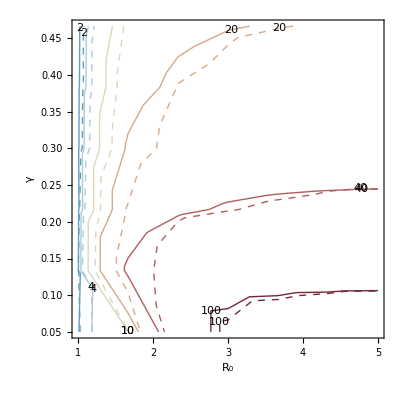

```mathematica
Show[SizePlot[grid[emMeanSamp,1000,tMax/.parsTest,3,1],{Thick}],SizePlot[grid[stoMeanSamp,1000,tMax/.parsTest,3,1],{Dashed}]]
```

```mathematica
Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/manuscript/Figures/k1000.png",%]
```

/Users/siavashriazi/Dropbox/Apps/Overleaf/manuscript/Figures/k1000.png

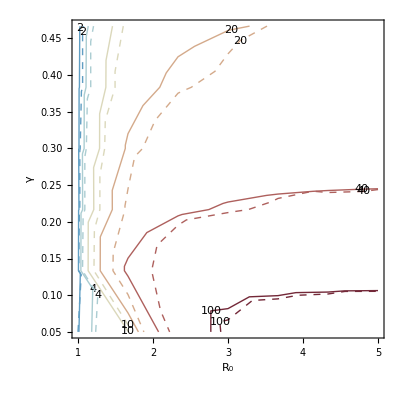

```mathematica
Show[SizePlot[grid[emMeanSamp,1000,tMax/.parsTest,3,1],{Thick}],SizePlot[grid[stoMeanSamp,1000,tMax/.parsTest,3,1],{Dashed}]]
```

```mathematica
(*Comparison of mean of total infected*)
```

```mathematica
emMeanTot[RA_,g_,κIn_,tM_,i0in_,ρin_]:=Block[{parsSim},
parsSim={β->RA g,γ->g,ψ->(ψ/.parsTest),σ->0.001,κ->κIn,tMax->tM,i0->i0in,ρ->ρin};
Evaluate[M["b",t]/.EMNSol[parsSim]]/.t->tMax/.parsSim
]
```

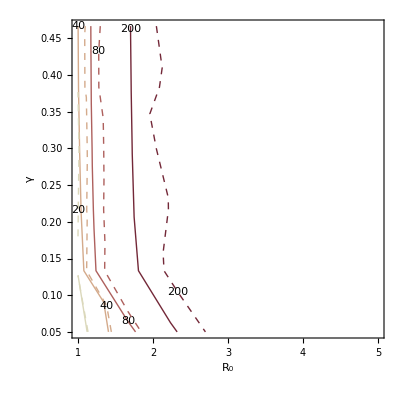

```mathematica
Show[SizePlot2[grid[emMeanTot,κ/.parsTest,tMax/.parsTest,i01,ρ/.parsTest],{Thick},2],SizePlot2[grid[stoMeanTot,κ/.parsTest,tMax/.parsTest,i01,ρ/.parsTest],{Dashed},2]]
```

#### Comparison of the Variance in Tree Size

```mathematica
emVarSamp[RA_,g_,κIn_,tM_,i0in_,ρin_]:=Block[{parsSim},
parsSim={β->RA g,γ->g,ψ->(ψ/.parsTest),σ->0.001,κ->κIn,tMax->tM,i0->i0in,ρ-> ρin};
Evaluate[V["l","l",t]/.EMNSol[parsSim]]/.t->tMax/.parsSim
]
```

```mathematica
emVarSamp[5,0.01,κ/.parsTest,100,i01,ρ01]
```

71.0604

```mathematica
(*Comparison of variances*)
```

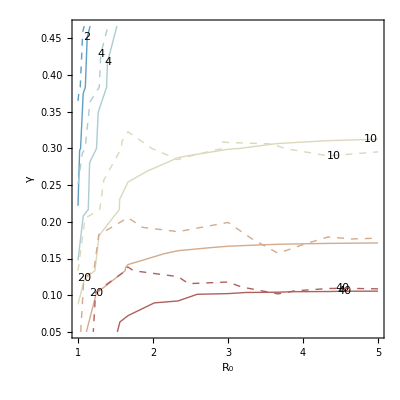

```mathematica
Show[SizePlot[grid[emVarSamp,κ/.parsTest,tMax/.parsTest,5,0],{Thick}],SizePlot[grid[stoVarSamp,κ/.parsTest,tMax/.parsTest,5,0],{Dashed}]]
```

```mathematica
Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/manuscript/Figures/var5.png",%]
```

/Users/siavashriazi/Dropbox/Apps/Overleaf/manuscript/Figures/var5.png

```mathematica
emVarTot[RA_,g_,κIn_,tM_,i0in_,ρin_]:=Block[{parsSim},
parsSim={β->RA g,γ->g,ψ->(ψ/.parsTest),σ->0.001,κ->κIn,tMax->tM,i0->i0in,ρ->ρin};
Evaluate[V["b","b",t]/.EMNSol[parsSim]]/.t->tMax/.parsSim
]
```

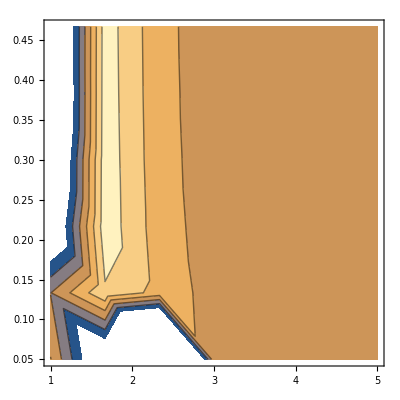

```mathematica
grid[emVarTot,κ/.parsTest,100,i01,ρ01]//ListContourPlot
```

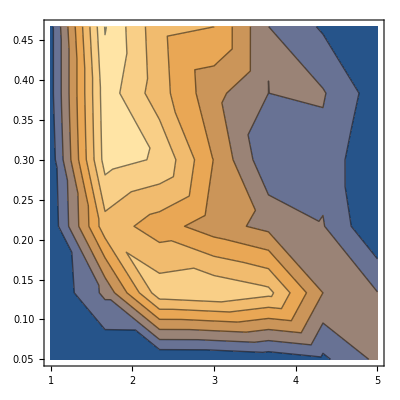

```mathematica
grid[stoVarTot,κ/.parsTest,100,i01,ρ01]//ListContourPlot
```

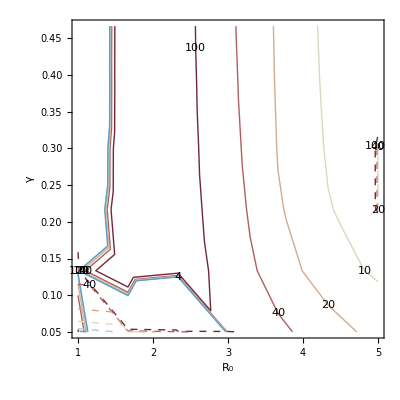

```mathematica
Show[SizePlot[grid[emVarTot,κ/.parsTest,100,i01,ρ01],{Thick}],SizePlot[grid[stoVarTot,κ/.parsTest,100,i01,ρ01],{Dashed}]]
```

```mathematica
emCVSamp[RA_,g_,κIn_,tM_,i0in_,ρin_]:=Block[{parsSim},
parsSim={β->RA g,γ->g,ψ->(ψ/.parsTest),σ->0.001,κ->κIn,tMax->tM,i0->i0in,ρ->ρin};
(Evaluate[V["l","l",t]/.EMNSol[parsSim]]/.t->tMax/.parsSim)/(Evaluate[M["l",t]/.EMNSol[parsSim]]/.t->tMax/.parsSim)
]
```

```mathematica
emCVSamp[5,0.01,κ/.parsTest,100,i01,ρ01]
```

4.86934

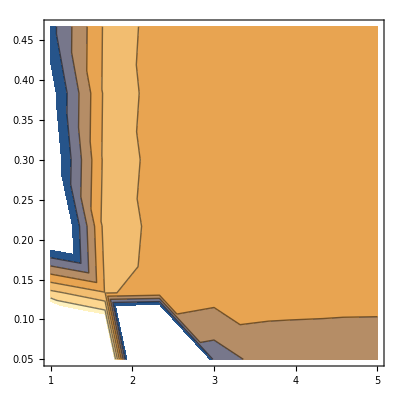

```mathematica
grid[emCVSamp,κ/.parsTest,100,i01,ρ01]//ListContourPlot
```

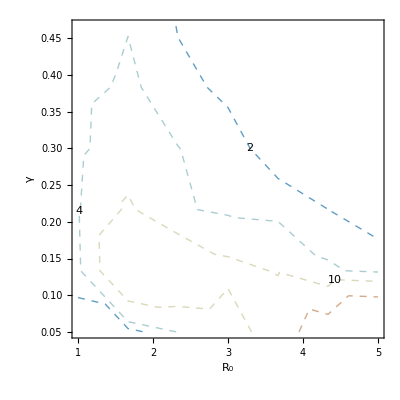

```mathematica
Show[SizePlot[grid[emCVSamp,κ/.parsTest,100,i01,ρ01],{Thick}],SizePlot[grid[stoCVSamp,κ/.parsTest,100,i01,ρ01],{Dashed}]]
```

```mathematica
emCVTot[RA_,g_,κIn_,tM_,i0in_,ρin_]:=Block[{parsSim},
parsSim={β->RA g,γ->g,ψ->(ψ/.parsTest),σ->0.001,κ->κIn,tMax->tM,i0->i0in,ρ->ρin};
(Evaluate[V["b","b",t]/.EMNSol[parsSim]]/.t->tMax/.parsSim)/(Evaluate[M["b",t]/.EMNSol[parsSim]]/.t->tMax/.parsSim)
]
```

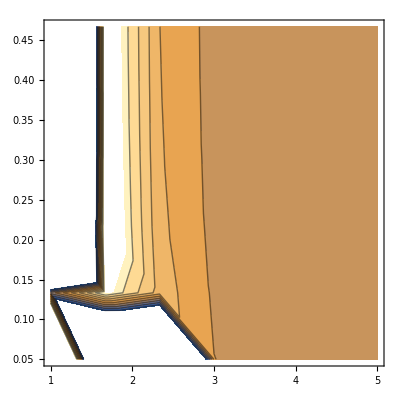

```mathematica
grid[emCVTot,κ/.parsTest,100,i01,ρ01]//ListContourPlot
```

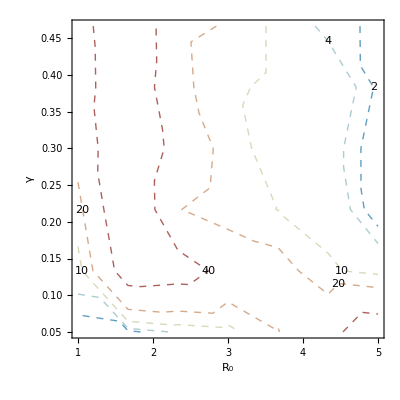

```mathematica
Show[SizePlot[grid[emCVTot,κ/.parsTest,100,i01,ρ01],{Thick}],SizePlot[grid[stoCVTot,κ/.parsTest,100,i01,ρ01],{Dashed}]]
```

```mathematica
RA1=4;g1=γ/.parsTest;k1=κ/.parsTest;tMax=tMax/.parsTest;i0in=3;ρin=1;
```

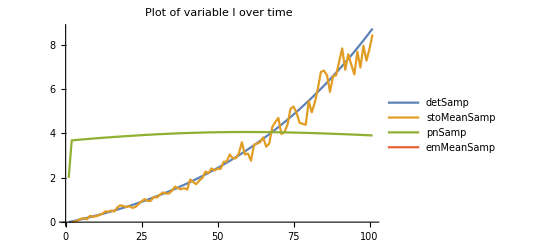

```mathematica
emMeanSampList=Table[emMeanSamp[RA1,g1,k1,t,i0in,ρin],{t,0,tMax}];
detSampList=Table[detSamp[RA1,g1,k1,t,i0in,ρin],{t,0,tMax}];
stoMeanSampList=Table[stoMeanSamp[RA1,g1,k1,t,i0in,ρin],{t,0,tMax}];
pnSampList=Table[pnSamp[RA1,g1,k1,t,i0in,ρin],{t,0,tMax}];
ListLinePlot[{detSampList,stoMeanSampList,pnSampList,emMeanSampList},PlotLegends->{"detSamp","stoMeanSamp","pnSamp","emMeanSamp"},FrameLabel->{"Time (tMax)","l"},PlotLabel->"Plot of variable l over time"]
```

```mathematica
emMeanSamp[3,0.01,300,20,3,0.5]
```

emMeanSamp[3,0.01,300,20,3,0.5]

```mathematica
emMeanSampList=Table[emMeanSamp[RA1,g1,k1,t,i0in,ρin],{t,0,tMax}];
```

```mathematica
Take[emMeanSampList,100]
```

Take::take: Cannot take positions 1 through 100 in Table[emMeanSamp[RA1,g1,k1,t,i0in,ρin],{t,0,tMax}].

Take[Table[emMeanSamp[RA1,g1,k1,t,i0in,ρin],{t,0,tMax}],100]

```mathematica
emMeanSampList2=Table[emMeanSamp[R0,g1,k1,100,i0in,ρin],{R0,1.,5.,4/6}];
```

```mathematica
stoMeanSampList2=Table[stoMeanSamp[R0,g1,k1,100,i0in,ρin],{R0,1.,5.,4/6}];
```

```mathematica
emMeanTotList2=Table[emMeanTot[R0,g1,k1,100,i0in,ρin],{R0,1.,5.,4/6}];
```

```mathematica
stoMeanTotList2=Table[stoMeanTot[R0,g1,k1,100,i0in,ρin],{R0,1.,5.,4/6}];
```

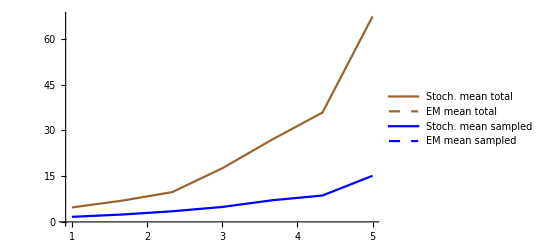

```mathematica
ListLinePlot[{stoMeanTotList2,emMeanTotList2,stoMeanSampList2,emMeanSampList2},PlotStyle->{{Thick,Brown},{Dashed,Brown},{Thick,Blue},{Dashed,Blue}},DataRange->{1,5},Frame->True,FrameLabel->{"R0","Value"},PlotLegends->{"Stoch. mean total","EM mean total","Stoch. mean sampled","EM mean sampled"}]
```

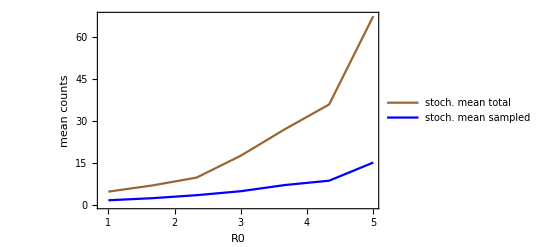

```mathematica
ListLinePlot[{stoMeanTotList2,stoMeanSampList2},PlotStyle->{{Thick,Brown},{Thick,Blue}},DataRange->{1,5},Frame->True,FrameLabel->{"R0","mean counts"},PlotLegends->{"stoch. mean total","stoch. mean sampled"}]
```

```mathematica
Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/manuscript/Figures/total_sampled_sto.png",%]
```

/Users/siavashriazi/Dropbox/Apps/Overleaf/manuscript/Figures/total_sampled_sto.png

#### Efficiency of different methods

```mathematica
Clear[nSampEM]
nSampEM[pars_]:=Evaluate[M["l",t]/.EMNSol[pars]]/.t->tMax/.pars
```

```mathematica
nSampVarEM[pars_]:=Evaluate[V["l","l",t]/.EMNSol[pars]]/.t->tMax/.pars
```

```mathematica
nSampEM[parsTest]
```

78.1376

```mathematica
Clear[nSampDistEM]
nSampDistEM[pars_]:=nSampDistEM[pars]=NormalDistribution[nSampEM[pars],Sqrt[nSampVarEM[pars]]]
```

```mathematica
Clear[nSampDet]
```

```mathematica
nSampDet[pars_]:=l[t]/.nsol[pars]/.t->tMax/.pars
```

```mathematica
nSampPn[pars_]:=Total[MapThread[Times,{test[parsTest,100],Table[i,{i,1,101}]}]]
```

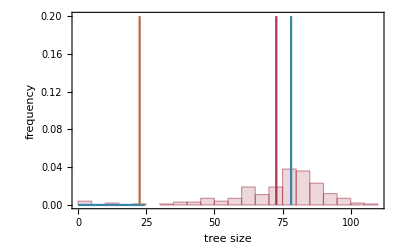

```mathematica
temp=Table[simInt[parsTest,intS,4][tMax/.parsTest],{intS,1,200}];
Show[
(*Simulation Data*)
Histogram[temp,20,"PDF",ChartStyle->Directive[{MyCol[[3]],Opacity[0.2]}]],
ListLinePlot[{{Mean[temp],0},{Mean[temp],0.2}},PlotStyle->MyCol[[3]]],
(*Ensemble Moment*)
ListLinePlot[{{nSampEM[parsTest],0},{nSampEM[parsTest],0.2}},PlotStyle->MyCol[[1]]],
Plot[PDF[nSampDistEM[parsTest],x],{x,0,30},PlotStyle->MyCol[[1]]],
(*Deterministic*)
ListLinePlot[{{nSampDet[parsTest],0},{nSampDet[parsTest],0.2}},PlotStyle->MyCol[[2]]],
ListLinePlot[{{nSampPn[parsTest],0},{nSampPn[parsTest],0.2}},PlotStyle->MyCol[[4]]],Frame->True,FrameLabel->{"tree size","frequency"}]
```

```mathematica
Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/manuscript/Figures/efficiency.png",%]
```

/Users/siavashriazi/Dropbox/Apps/Overleaf/manuscript/Figures/efficiency.png

```mathematica
nSampDet[parsTest]
```

l[100]

```mathematica
nSampPn[parsTest]
```

22.602